```mathematica
(*Here, we have to initialize the power absorbed by one period of oscillation*)
Ω  = 0;
ω0=   2;
γ1 = .1;
γ2 = .4;
f    = .1;
AT[ω_]:=-((2*Pi*ⅈ*f^2*ω)(ω0^2-ω^2-ⅈ*γ2*ω))/(((ω0^2-ω^2-ⅈ*γ1*ω)*(ω0^2-ω^2-ⅈ*γ2*ω))-Ω^4)
AT1[ω_,Ω_]:=-((2*Pi*ⅈ*f^2*ω)(ω0^2-ω^2-ⅈ*γ2*ω))/(((ω0^2-ω^2-ⅈ*γ1*ω)*(ω0^2-ω^2-ⅈ*γ2*ω))-Ω^4)
Dis[t_,ω_,Ω_]:=((ω0^2-ω^2-ⅈ*γ2*ω)*f*Exp[-ⅈ*ω*t])/(((ω0^2-ω^2-ⅈ*γ1*ω)*(ω0^2-ω^2-ⅈ*γ2*ω))-Ω^4)
```

```mathematica
FinalAnimation=Animate[Plot[Re[AT1[x,Ω]],{x,-5,5},PlotRange->{{0,4},{0,.7}},Frame->True,FrameLabel->{"Detuning" ,"Absorbed Probe Power"},PlotLabel->"Autler-Townes Doublet",PlotTheme->"Scientific",FrameStyle->Directive[GrayLevel[0],Thickness[Medium]]],{Ω,0,3},AnimationRunning->False]
```

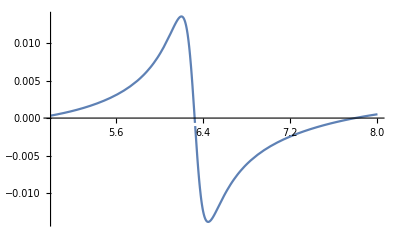

```mathematica
finplt3=Plot[Re[Dis[1,ω,6]],{ω,5,8},PlotRange->Automatic]
```

```mathematica
Dis[0,0,.1]
```

0.0250002+0. ⅈ

```mathematica
FinalAnimationEIT=Animate[Plot[Re[Dis[t,ω,6]],{ω,4,8},PlotRange->{{4,8},{-.15,.15}},Frame->True,FrameLabel->{"Frequency" ,"Dispersion"},PlotLabel->"Electromagnetically Induced Transparency",PlotTheme->"Scientific",FrameStyle->Directive[GrayLevel[0],Thickness[Medium]]],{t,0,3},AnimationRunning->False]
```

```mathematica
Export["EIT Simulation.jpg",FinalPlot]
```

EIT Simulation.jpg

```mathematica
Export["Final Animation.gif",FinalAnimation]
```

Final Animation.gif

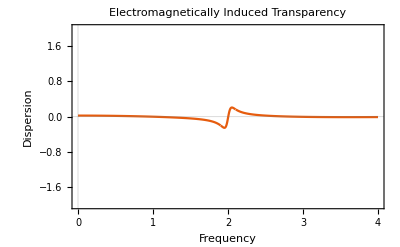

```mathematica
Plot[Re[Dis[1.6,ω,.1]],{ω,0,4},PlotRange->{{0,4},{-2,2}},Frame->True,FrameLabel->{"Frequency" ,"Dispersion"},PlotLabel->"Electromagnetically Induced Transparency",PlotTheme->"Scientific",FrameStyle->Directive[GrayLevel[0],Thickness[Medium]]]
```

```mathematica
FinalAnimationEITTEST=Animate[Plot[Re[Dis[t,ω,.1]],{ω,-10,10},PlotRange->{{0,4},{-3,3}},Frame->True,FrameLabel->{"Frequency" ,"Dispersion"},PlotLabel->"Electromagnetically Induced Transparency",PlotTheme->"Scientific",FrameStyle->Directive[GrayLevel[0],Thickness[Medium]]],{t,0,3},AnimationRunning->False]
```

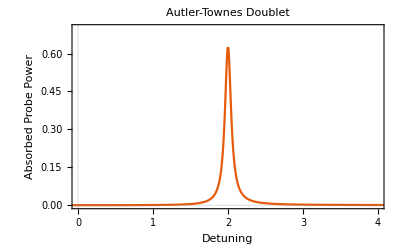

```mathematica
finalplt1=Plot[Re[AT1[x,Ω]],{x,-5,5},PlotRange->{{0,4},{0,.7}},Frame->True,FrameLabel->{"Detuning" ,"Absorbed Probe Power"},PlotLabel->"Autler-Townes Doublet",PlotTheme->"Scientific",FrameStyle->Directive[GrayLevel[0],Thickness[Medium]]]
```

```mathematica
Export["EIT Dispersion.jpg", finplt3]
```

EIT Dispersion.jpg